#### Initialization cells

```mathematica
Unprotect[Internal`EncodeCharacters];
Internal`EncodeCharacters[str_,enc_]:=Quiet[FromCharacterCode[ToCharacterCode[str],enc]]
NotebookDirectory[]
```

#### Background and smoothing

Eiler’s  algorithm for background calculation [1] and data smoothing [2].

```mathematica
(* original version
smooth[data_,lambda_,order_]:=Module[{y=data,λ=lambda,o=order},Clear[f];
m=Length[y];
e=IdentityMatrix[m];
d=Differences[e,o];
f=LinearSolve[(e+N[λ] dᵀ.d)];Clear[m,e,d];f[N[y]]];
*)
```

```mathematica
smooth[data_,lambda_:0.5*10^3,order_:3]:=Module[{λ=N@lambda,o=order,m,e,d,f,y},
(*1D case:data is a vector*)
If[VectorQ[data,NumericQ],y=N@data;
m=Length@y;
e=IdentityMatrix[m];
d=Differences[e,o];
f=LinearSolve[e+λ Transpose[d].d];
Return[f[y]];];
(*2D case:data is {{x,y},...}->smooth only y and keep x*)If[MatrixQ[data,NumericQ]&&Dimensions[data][[2]]==2,y=N@data[[All,2]];
m=Length@y;
e=IdentityMatrix[m];
d=Differences[e,o];
f=LinearSolve[e+λ Transpose[d].d];
Return[Transpose@{data[[All,1]],f[y]}];];
(*otherwise*)
$Failed]
```

```mathematica
(* original version
bckgrnd[ydata_,weight_,lambda_,iterations_]:=Module[{y=ydata,p=weight,λ=lambda, it=iterations},
m=Length[y];Clear[z];
dff=Differences[IdentityMatrix[m],2];
w=ConstantArray[1,m];
Table[W=DiagonalMatrix[w];
cho=CholeskyDecomposition[W+N[λ]dffᵀ.dff];
z=LinearSolve[cho,LinearSolve[choᵀ,w y]];
w=Array[N@p Boole[y[[#]]>z[[#]]]&,Length[y]]+Array[(1-N@p)Boole[y[[#]]<z[[#]]]&,Length[y]];,{i,it}];Clear[y,p,λ,m,w,dff,W,cho, it]; z]
*)
```

```mathematica
bckgrnd[data_,weight_:5*10^-3,lambda_:10^5,iterations_:10]:=Module[{p=weight,λ=lambda,it=iterations,y,x,m,z,dff,w,W,cho},{x,y}=If[VectorQ[data],{None,data},{data[[All,1]],data[[All,2]]}];
m=Length[y];Clear[z];
dff=Differences[IdentityMatrix[m],2];
w=ConstantArray[1,m];
Table[W=DiagonalMatrix[w];
cho=CholeskyDecomposition[W+N[λ] dffᵀ.dff];
z=LinearSolve[cho,LinearSolve[choᵀ,w y]];
w=Array[N@p Boole[y[[#]]>z[[#]]]&,m]+Array[(1-N@p) Boole[y[[#]]<z[[#]]]&,m];,{i,it}];
If[x===None,z,Transpose@{x,z}]]
```

#### Graphic style functions

working version with two classical sides and top

```mathematica
labels[xaxes_,yaxes_,plotlabel_,panellabel_,offset_]:=Module[{xa=xaxes,ya=yaxes,plbl=plotlabel,panlbl=panellabel,off=offset},
Clear[out];out={Text[Style[xa,fs,FontFamily->"Arial"],Offset[{0,0},Scaled[{0.5,-off[[1]]}]]],Text[Rotate[Style[ya,fs,FontFamily->"Arial"],π/2],Offset[{0,0},Scaled[{-off[[2]],0.5}]]],Text[Style[plbl,fs,FontFamily->"Arial"],Offset[{0,0},Scaled[{0.5,1.+0.5 off[[2]]}]]],Text[Style[If[panlbl=="","",panlbl],2fs,Bold,FontFamily->"Arial"],Scaled[{0.1,0.9}]]};Clear[xa,ya,plbl];out]
```

with two classical sides

```mathematica
labels2[xaxes_,yaxes_,panellabel_,offset_,fontsize_]:=Module[{xa=xaxes,ya=yaxes,panlbl=panellabel,off=offset,fsz=fontsize},
Clear[out];out={Text[Style[xa,fsz,FontFamily->"Arial"],Offset[{0,0},Scaled[{0.5,-off[[1]]}]]],Text[Rotate[Style[ya,fsz,FontFamily->"Arial"],π/2],Offset[{0,0},Scaled[{-off[[2]],0.5}]]],Text[Style[If[panlbl=="","",panlbl],2fsz,Bold,FontFamily->"Arial"],Scaled[{0.1,0.9}]]};Clear[xa,ya];out]
```

with four sides

```mathematica
labels4[xbottom_,xtop_,yleft_,yright_,panellabel_,offset_]:=Module[{xb=xbottom,xt=xtop,yl=yleft,yr=yright,panlbl=panellabel,off=offset},
Clear[out];out={Text[Style[xb,fs,FontFamily->"Arial"],Offset[{0,0},Scaled[{0.5,-off[[1]]}]]],Text[Style[xt,fs,FontFamily->"Arial"],Offset[{0,0},Scaled[{0.5,1.+off[[1]]}]]],Text[Rotate[Style[yl,fs,FontFamily->"Arial"],π/2],Offset[{0,0},Scaled[{-off[[2]],0.5}]]],Text[Rotate[Style[yr,fs,FontFamily->"Arial"],-π/2],Offset[{0,0},Scaled[{1.+off[[2]],0.5}]]],Text[Style[If[panlbl=="","",panlbl],2fs,Bold,FontFamily->"Arial"],Scaled[{0.1,0.9}]]};Clear[xb,yl,yr];out]
```

Line style function for fast generation of styles with thickness,

```mathematica
linstl[color_,linestyle_,thickness_]:=Directive[color,linestyle,AbsoluteThickness[thickness]]
Attributes[linstl]=Listable
```

Listable

Graphics inset function

```mathematica
sh[graph_]:=Graphics@Inset[graph]
```

#### Statistical functions

Sample size estimate

```mathematica
Φ[rv_]=CDF[NormalDistribution[0,1],rv];
iΦ[rv_]=InverseCDF[NormalDistribution[0,1],rv];
ess[alpha_,beta_,sample1_,sample2_]:=Module[{al=alpha,bt=beta,sm1=sample1,sm2=sample2},μ1=Mean[sm1];μ2=Mean[sm2];σ1=StandardDeviation[sm1];σ2=StandardDeviation[sm2];
n1=Length[sm1];
n2=Length[sm2];
σp=√(((n1-1)σ1^2+(n2-1)σ2^2)/(n1+n2-2));ns=Round@(((iΦ[1-al/2]+iΦ[1-bt])/(Abs[μ1-μ2]/σp))^2)]
```

#### Dynamic light scattering

DLS files data extraction function for simple export of intensities and sizes and single file

```mathematica
dls[filename_]:=Module[{fni=filename},Clear[data,size,int,vol,corr];data=Import[fni,"TSV"]ᵀ;size=Cases[data,{x_/;StringMatchQ[x,"S"~~___~~")"] ,_}]ᵀ[[2]];int=Cases[data,{x_/;StringMatchQ[x,"I"~~___~~")"] ,_}]ᵀ[[2]];vol=Cases[data,{x_/;StringMatchQ[x,"V"~~___~~")"] ,_}]ᵀ[[2]];corr=Cases[data,{x_/;StringMatchQ[x,"C"~~___~~"]"] ,_}]ᵀ[[2]];{{size,int}ᵀ,{size,vol}ᵀ,corr,Max[corr]}]
```

DLS files data extraction function for simple export of intensities and sizes and single file with different output parameters

```mathematica
dlss[filename_]:=Module[{fni=filename},Clear[data,size,int,vol,corr];data=Import[fni,"TSV"]ᵀ;size=Cases[data,{x_/;StringMatchQ[x,"S"~~___~~")"] ,_}]ᵀ[[2]];int=Cases[data,{x_/;StringMatchQ[x,"I"~~___~~")"] ,_}]ᵀ[[2]];vol=Cases[data,{x_/;StringMatchQ[x,"V"~~___~~")"] ,_}]ᵀ[[2]];corr=Cases[data,{x_/;StringMatchQ[x,"C"~~___~~"]"] ,_}]ᵀ[[2]];{size,int,corr,Max[corr]}]
```

DLS  files data extract for preconfigured export in Malvern with size/intensity and autocorrelation/time data and multiple entries.

```mathematica
dlsm[filename_]:=Module[{datar,data,snam,size,int,corrdel,corr},datar=Import[filename,"TSV"];
data=Transpose[Take[#,Length[datar[[1]]]]&/@datar];
snam=Drop[data[[2]],1];
size=Drop[Cases[data,Join[{x_/;StringMatchQ[x,"Size"~~___~~")"]} ,ConstantArray[_,Length[dataᵀ]-1]]]ᵀ,1];int=Drop[Cases[data,Join[{x_/;StringMatchQ[x,"Int"~~___~~")"]} ,ConstantArray[_,Length[dataᵀ]-1]]]ᵀ,1];corrdel=Drop[Cases[data,Join[{x_/;StringMatchQ[x,"Correlation Delay"~~___~~")"]} ,ConstantArray[_,Length[dataᵀ]-1]]]ᵀ,1];corr=Drop[Cases[data,Join[{x_/;StringMatchQ[x,"Correlation Data"~~___~~"]"]} ,ConstantArray[_,Length[dataᵀ]-1]]]ᵀ,1];{snam,size,int,corrdel,corr}]
```

#### Mass photometry

Average molecular weight from mass photometry distribution.

```mathematica
Mwa[distribution_,molecularweight_]:=Module[{dist=distribution,Mw=molecularweight},freq=BinCounts[Round@(dist/Mw),{0,Max@(dist/Mw),1}];M=N@(Sum[freq[[i]] i^2,{i,Length[freq]}]/Sum[freq[[i]]i,{i,Length[freq]}])]
```

#### Fractal crossover size

This function estimates where scattering crosses over from the Rayleigh regime to the fractal power - law regime for a given measurement geometry . It returns the aggregate size, aggregation number, and characteristic DLS time .

```mathematica
CrossoverFractal[R0NM_?NumericQ,(*monomer radius in nm*)Df_?NumericQ,lambdaNM_?NumericQ,(*wavelength nm*)thetaDeg_?NumericQ,(*scattering angle*)n_:1.33           (*refractive index*)]:=Module[{kB=1.380649*10^-23,T=296,eta=0.001,lambda,theta,q,RgNM,N,D,tau},lambda=lambdaNM*10^-9;
theta=thetaDeg*Degree;
q=(4 Pi n/lambda)*Sin[theta/2];
(*crossover*)RgNM=(1/q)*10^9;
(*aggregation number*)N=(RgNM/R0NM)^Df;
(*DLS time*)D=kB T/(6 Pi eta RgNM*10^-9);
tau=1/(D q^2);
<|"Rg_nm"->RgNM,"N"->N,"tau_s"->tau|>]
```

#### Various data manipulation

Halftime function

```mathematica
htf[kinetictrace_,midvalue_:0.5]:=Module[{lst=kinetictrace,mv=midvalue,list},list=Transpose@{lst[[All,1]],Rescale@lst[[All,2]]};
First@Cases[list,{_,First@Nearest[list[[All,2]],mv]}]]
```

Take every n^th sample of a list.

```mathematica
thin[list_,interval_]:=list[[1;;-1;;interval]]
```

Position function finds a position of a value in a one dimensional list

```mathematica
lps[list_,value_,number_:1]:=First@Flatten[Position[list,First@Nearest[list,N@value,number]]]
```

Quantity magnitude function, it returns the magnitude of the quantity with units.

```mathematica
qm[x_]:=QuantityMagnitude[x];
SetAttributes[qm,Listable];
```

Function that transform x and y values in 2D list, can use the functional form:
#^3 &. xySc[data, #^3 &, 1]

```mathematica
xySc[data2D_,xSpec_:Identity,ySpec_:Identity]:=Module[{xs=data2D[[All,1]],ys=data2D[[All,2]],xF,yF},xF=Which[Head[xSpec]===Function,xSpec,NumericQ[xSpec],(xSpec #)&,True,Identity];
yF=Which[Head[ySpec]===Function,ySpec,NumericQ[ySpec],(ySpec #)&,True,Identity];
Transpose[{xF/@xs,yF/@ys}]]
```

#### Atomic Force Microscopy functions

AFM color-map function

```mathematica
afmHot=RGBColor[2 #,2 #-.5,2 #-1]&;
```

JPK AFM height data .txt to .png images export function

```mathematica
imgjpkex[filename_,range_,smoothing_]:=Module[{fn=filename,rng=range,smth=smoothing},ClearAll[a,as,mas,af,ai,pars,res];
res=Take[Import[fn,"Table"],18][[8,3]];
a=10^9 Drop[Import[fn,"Table"],18];
as=smooth[#,First@smth,Last@smth]&/@a;
mas=Median[Flatten[as]];
af=as-mas;
pars={ColorFunction->(afmHot[Rescale[#1,rng]]&),ColorFunctionScaling->False};
ai=ReliefImage[af,ColorFunction->(afmHot[Rescale[#1,rng]]&),ColorFunctionScaling->False,Method->"DiffuseReflection"];
Export[StringTake[fn,{1,-4}]<>"png",ai]]
```

JPK AFM height data visualisation

```mathematica
imgjpk[filename_,range_,smoothing_]:=Module[{fn=filename,rng=range,smth=smoothing},ClearAll[a,as,mas,af,ai,pars,res];
res=Take[Import[fn,"Table"],18][[8,3]];
a=10^9 Drop[Import[fn,"Table"],18];
as=smooth[#,First@smth,Last@smth]&/@a;
mas=Median[Flatten[as]];
af=as-mas;
pars={ColorFunction->(afmHot[Rescale[#1,rng]]&),ColorFunctionScaling->False};
ai=ReliefImage[af,ColorFunction->(afmHot[Rescale[#1,rng]]&),ColorFunctionScaling->False,Method->"DiffuseReflection"]]
```

JPK auxiliary data from .txt

```mathematica
auxjpk[filename_]:=Module[{fn=filename},Clear[resolution,offset,date];resolution=Take[Import[fn,"Table"],18][[8;;9,3]];
offset=Take[Import[fn,"Table"],18][[6;;7,3]];
size=Take[Import[fn,"Table"],18][[4;;5,3]];
date=Take[Import[fn,"Table"],18][[14,4;;8]];{resolution,offset,size,date}]
```

JPK height data from txt

```mathematica
hjpk[filename_]:=Module[{fn=filename},Clear[height];
height=10^9 Drop[Import[fn,"Table"],18];height]
```

#### Protein charge vs pH

The function to calculate the charge vs pH from protein sequence. The aam function returns values of pKa from the database file aa_pKa.nb based on reference data from many proteins. The second one computes charge and absolute charge, i.e. negative and positive values vs positive values.

```mathematica
aam[data_,code_String]:=Module[{entry},entry=SelectFirst[data,#[[1]]===code&];
If[entry=!=Missing["NotFound"],First[entry[[3]]],Missing["NoMatch"]]]
```

```mathematica
chsq[sequence_,data_,phshift_,ph_]:=Module[{seq=sequence,d=data,dpH=phshift,pH=ph},
Clear[aa,q0,aac,aan,aach,aps,q,acid,base,f,charge,chden];
aa={"C","Y","D","E","K","R","H"};
q0={-1,-1,-1,-1,1,1,1};
aac=Evaluate[StringCases[seq,#]&/@aa];
aan=Length[#]&/@aac;
aach=DeleteDuplicates[Flatten@aac];
aps=Flatten[Position[aa,#]&/@aach];
q=q0[[aps]];
acid[pKa_,pH_]=N@(10^(pH-pKa)/(10^(pH-pKa)+1));
base[pKa_,pH_]=N@(10^(pKa-pH)/(10^(pKa-pH)+1));
f[pKa_,q_,pH_]:=If[q<0,acid[pKa+dpH,pH],base[pKa+dpH,pH]];
charge[pH_]:=Sum[aan[[i]]q[[i]]f[aam[d,aach[[i]]],aan[[i]]q[[i]],pH],{i,Length[q]}]+base[aapka[[8,3]][[1]],pH]+acid[aapka[[9,3]][[1]],pH];
chden[pH_]:=Abs@Sum[aan[[i]]q[[i]]f[aam[d,aach[[i]]],aan[[i]]q[[i]],pH],{i,Length[q]}]+Abs@base[aapka[[8,3]][[1]],pH]+Abs@acid[aapka[[9,3]][[1]],pH];{charge[pH],chden[pH]}]
```

#### FreeSASA functions

Extracting total area from base output of freeSASA program, file name as input.

```mathematica
freeSASAbasetot[file_String]:=Module[{text,match},text=Import[file,"Text"];
match=StringCases[text,RegularExpression["Total\\s*:\\s*([0-9]+\\.?[0-9]*)"]:>ToExpression["$1"]];
If[match=!={},First[match],Missing["NoMatch"]]]
```

#### pH conversion function

Functions for conversion of pH values from measured temperature (RT) with given temperature correction coefficient (dT) to desired temperature FT.

```mathematica
fromRT[ph_,RT_,dT_,FT_]:=Round[ph-Abs[FT-RT]dT,0.01];
toRT[ph_,RT_,dT_,FT_]:=Round[ph+Abs[FT-RT]dT,0.01];
```

#### Concentration from FTIR Absorbance

Absorbance at Amide I band corresponds to peptide bond, hence molecular weight of the protein and number of residues required. ϵ_p=950 [L mol^-1 cm^-1].

```mathematica
cuf[absorbanceFtir_,extinction_,pathlength_,molecularweight_,Nresidues_]:=Module[{A=absorbanceFtir,epd=extinction,l=pathlength,mw=molecularweight,nr=Nresidues},UnitConvert[A/(epd l)1/(2 nr-1)mw,"Milligrams"/"Milliliters"]];
```

#### Styles and frontend

log tick labeling

```mathematica
logTicks[min_,max_]:=Table[{10^i,Superscript[10,i]},{i,Ceiling[Log10[min]],Floor[Log10[max]]}]
```

styles of the graph

```mathematica
SetOptions[$FrontEnd,PrintingStyleEnvironment->"Working"]
fs=6;
is=85/25.4 72;
style={Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[0.5]],LabelStyle->Directive[Black,fs,FontFamily->"Arial"],PlotRangeClipping->None,ImagePadding->{{25,10},{25,20}},PlotRangeClipping->Automatic ,PlotRangePadding->Automatic,AspectRatio->1};
sym={"●","■","◆","▲","▼","○","□","◇","△","▽"};
impd=ImagePadding->{{25,10},{25,10}};
impd2=ImagePadding->{{25,5},{25,5}};
impd4=ImagePadding->{{25,25},{25,25}};
δ=AbsoluteThickness[0.5];
dashed=AbsoluteDashing[{6,2}];
dotted=AbsoluteDashing[{2,2}];
```

#### References

[1] P. H. Eilers and H. F. Boelens. Baseline correction with asymmetric least squares smoothing. Technical report, Leiden University Medical Centre Report, 2005.
[2] P. H. C. Eilers. A perfect smoother. Analytical Chemistry, 75(14):3631–3636, 2003.

#### Examples

Frame labels on all four sides

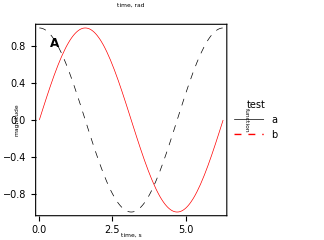

```mathematica
leg=LineLegend[linstl[{Black,Red},{None,Dashed},{0.5,1.}],{"a","b"},LegendMarkerSize->{20,1},LegendLabel->Style["test",Bold],LabelStyle->fs];
Plot[{Sin[x],Cos[x]},{x,0,2π},ImageSize->is,Evaluate[impd4],Evaluate[style],PlotStyle->linstl[{Red,Black},{None, Dashed},{0.5,0.5}],Epilog->{labels4["time, s","time, rad","magnitude","function","A",{0.1,0.1}],Inset[leg,Scaled[{0.6,0.8}]]},FrameTicks->{{Automatic,Range[-1,1,0.5]},{Automatic,{0,{π/2,"A",{1,0.},Dashed},π,3π/2,2π}}},Axes->False]
Clear[leg]
```

Styles

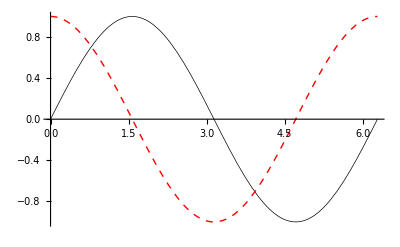

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π},PlotStyle->linstl[{Black,Red},{None,Dashed},{0.5,1.0}]]
```

Estimating  sample size from

```mathematica
Table[smpl=2;ess[0.05,0.2,RandomReal[{1.5,2.5},smpl],RandomReal[{2.0,3.0},smpl]],1000];
Select[%,#<=smpl&];
Length[%]
Clear[smpl]
```

540

Generating test data, calculating and plotting the background

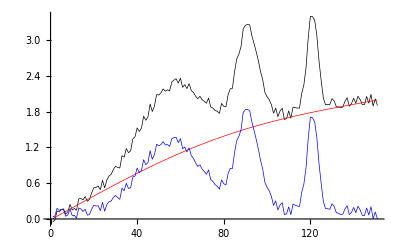

```mathematica
y=N@Table[2Sin[5 10^-2 x]+9 PDF[NormalDistribution[11,3],x]+4PDF[NormalDistribution[18,1],x]+2PDF[NormalDistribution[24,0.5],x]+RandomReal[{-0.1,0.1}],{x,0,30,0.2}];
b=bckgrnd[y,0.009,1. 10^5,10];
ListLinePlot[{y,b,y-b-Min[y-b]},PlotStyle->linstl[{Black,Red,Blue},{None,None,None},0.5]]
Clear[b,y]
```

Protein charge calculation

```mathematica
seq=ProteinData["S100A9","Sequence"];
aad={{"D","Asp",Around[3.5228057553956833,1.1790828103190307]},{"E","Glu",Around[4.188104575163399,0.9037515026077535]},{"H","His",Around[6.550763358778625,1.016799366277575]},{"C","Cys",Around[6.83,2.749433274937461]},{"Y","Tyr",Around[10.2965,1.1895079699297166]},{"K","Lys",Around[10.463714285714286,1.069387085902854]},{"R","Arg",Around[13.799999999999999,0.10000000000000053]},{"N-term","N-term",Around[7.655625,0.5476369691684448]},{"C-term","C-term",Around[3.299545454545455,0.7722106625521998]}};
Plot[Evaluate[chsq[seq,aad,x]],{x,0,14},PlotStyle->linstl[{Black, Red},{None,Dashed},0.5]]
Clear[seq,aad]
```

Correcting the HEPES buffer pH from 23 to 37 °C, dT=0.014 (°C)^-1.

```mathematica
fromRT[{6.81,7.3,7.6,7.76,8.25},23,0.014,37]
```

{6.61,7.1,7.4,7.56,8.05}

```mathematica
CrossoverFractal[4, 1.6,488,180]
CrossoverFractal[4, 1.6,658,173]
CrossoverFractal[4, 1.6,690,90]
CrossoverFractal[4, 1.6,350,90]
```

<|Rg_nm→29.1984,N→24.059,tau_s→0.000114816|>

<|Rg_nm→39.4435,N→38.9282,tau_s→0.000283043|>

<|Rg_nm→58.3852,N→72.9102,tau_s→0.000917981|>

<|Rg_nm→29.6157,N→24.6115,tau_s→0.000119809|>